```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

## n \mapsto t[n] is defined as a table in myFunctionsPureCodeV8 copy.nb, whhich is loaded by myFunctionsMathematica8.m. The table was created in my2ndEditOdlyzkoAccrtZrs6dec15.nb. It is from a table on Odlyzko’s site.

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

```mathematica
streem=OpenWrite["cardioidfx4rho2spiral9mar16no2"];
zeros={bestzero[2]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem];
el=Length[zeros];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=zeros[[j]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

```mathematica
strm=OpenRead["2000 better zeros copy 2"];
zrs=ReadList[strm];
zero[n_]:=zrs[[n]]
```

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

```mathematica
showData[data_]:=Print[Graphics[Raster[data]]]
```

```mathematica
pairToComplex[pair_]:=pair[[1]]+I*pair[[2]]
```

```mathematica
Map[pairToComplex,{{1,2},{3,4}}]
```

{1+2 ⅈ,3+4 ⅈ}

```mathematica
pairsetToComplexset[pairset_]:=Map[pairToComplex,pairset]
```

```mathematica
column[n_,matrix_]:=matrix[[All,n]]
```

```mathematica
mtrx={{1,2},{3,4},{5,6}};MatrixForm[mtrx]
```

(1 | 2
3 | 4
5 | 6)

```mathematica
column[1,%]
```

{1,3,5}

```mathematica
column[2,%%]
```

{2,4,6}

```mathematica
strm=OpenRead["zeros10^5odlyzko.txt"];
longzrs=ReadList[strm];
longzero[n_]:=.5+longzrs[[n]]*I
```

```mathematica
signsNoGraphics11[f_,center_,searchradius_,grain_,resolution_]:=
Module[{dta,row,shade,j,k,inc,m,w,seed,escape,green,white,blue,red,yellow,purple,aqua,black,orange,palegreen,u,v},
inc=searchradius/grain;
dta={};
black={0,0,0};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
white={1,1,1};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
w=N[center+j+k*I];
u=Re[f[w]];
v=Im[f[w]];
shade=white;
If[Abs[u-.5]<resolution,shade=red];

row=Append[row,shade];

];
dta=Append[dta,row];
];

Return[dta]
]
```

```mathematica
need:
```

```mathematica
signsNoGraphics10[f_,center_,searchradius_,grain_]:=
Module[{dta,row,shade,j,k,inc,m,w,seed,escape,green,white,blue,red,yellow,purple,aqua,black,orange,palegreen,u,v},
inc=searchradius/grain;
dta={};
black={0,0,0};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
white={1,1,1};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
w=N[center+j+k*I];
u=Re[f[w]];
v=Im[f[w]];
shade=black;
If[u>0,If[v>0,shade=blue]];
If[u>0,If[Not[v>0],shade=green]];
If[u<0,If[v>0,shade=red]];
If[u<0,If[Not[v>0],shade=yellow]];


row=Append[row,shade];

];
dta=Append[dta,row];
];

Return[dta]
]
```

```mathematica
zeta1[z_]:=Module[{k,w,answer},
w=z;
For[k=0,k<1,k++;w=Zeta[w];
If[Abs[w]>10^8,Break[]];
If[Abs[w-1]<1/10^8,Break[]];

];
Return[w]];
z=0;
For[n=0,n<50,n++;z=N[zeta1[z]]];phi=z;
```

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

```mathematica
need:
```

```mathematica
phibasin[center_,searchradius_,lowbound_,grain_,escaperatio_,depth_]:=
Module[{row,shade,j,k,inc,m,n,w,seed,color,blue,green,yellow,red,white,black,dta,phi},
phi=0;For[n=0,n<50,n++;phi=N[Zeta[phi]]];
inc=searchradius/grain;
dta={};
black={0,0,0};
white={1,1,1};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
seed=N[center+j+k*I];
m=0;
w=seed;
color=white;
While[m<depth,m++;
outm=m;
w=N[Zeta[w]];
If[Abs[w-1]<lowbound*Abs[seed - 1],Break[]];
If[Abs[w]>escaperatio*Abs[seed],Break[]];
If[Abs[w-phi]<lowbound*Abs[seed - phi],color=black;Break[]]
];

row=Append[row,color]];
dta=Append[dta,row];
];


Return[dta]
]
```

```mathematica
arg[z_]:=Module[{answer},
answer=Arg[z];
If[Arg[z]<0,answer=Arg[z]+2*Pi];
Return[answer]];
Attributes[arg]=Listable
```

Listable

```mathematica
minimize[f_,center_,range_,grain_]:=
Module[{best,j,k,inc,seed,start},
start=SessionTime[];
inc=range/grain;
best={center,f[center]};
For[k=-range/2-inc,k<range/2,k=k+inc;
kminimize=k;
row={};
For[j=-range/2-inc,j<range/2,j=j+inc;
jminimize=j;
seed=center+j+k*I;


If[f[seed]<best[[2]],best={seed,f[seed]}];

]
];
Return[best]

]
```

```mathematica
zeroFinder5[f_,startcenter_,startrange_,rangedivider_,grain_,depth_]:=
Module[{g,j,m,mz,s,best,oldmz,newrange,newcenter},
best={Infinity,Infinity};
g[s_]:=Abs[f[s]];
newrange=startrange;
newcenter=startcenter;
For[m=0,m<depth,m++;
outm=m;
mz=minimize[g,newcenter,newrange,grain];
If[Not[Abs[mz[[2]]]<best[[2]]],Return[best]];
If[Abs[mz[[2]]]<best[[2]],
best=mz;
newrange=newrange/rangedivider;
newcenter=best[[1]]]];
Return[best]]
```

```mathematica
f[s_]:=zetaIterate[s,1]-s;
highbound=10^8;
lowbound=1/10^8;
center=-14.5+3*I;
searchradius=5;
grain=500;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

-Graphics-

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

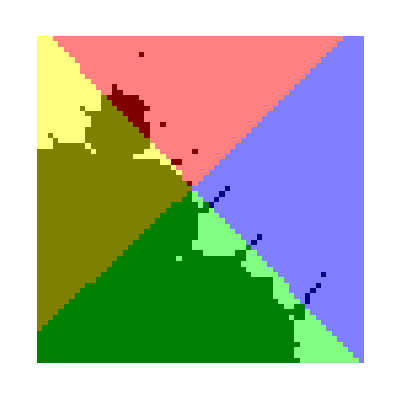

```mathematica
f[s_]:=zetaIterate[s,1]-s;
highbound=10^8;
lowbound=1/10^8;
center=-14.613+3.1*I;
searchradius=.01;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

```mathematica
precision=500;
f[s_]:=zetaIterate[s,1]-s;
startrange=.02;
rangedivider=2;
grain=20;
depth=20;
startcenter=-14.613+3.1*I;
fx=zeroFinder5[f,startcenter,startrange,rangedivider,grain,depth];
fxx=FindRoot[f[s],{s,fx[[1]]},WorkingPrecision->precision][[1,2]];
Print["fixed point   "];
Print[fxx];
Print["error"];
Print[zetaIterate[fxx,1]-fxx]
```

fixed point

-14.613492351835987588071919186650501218747528736282229780692263991054063766791532187998788325523331299779947660927059268843558369830085036285417306639829496147778125412237699024941461534617687776065523538231789771841059401301123142696724057582255278560119642875859519283572093307831395693679030738041585549045672902717355879685073468233856437440052748378467994913740479476433339993090730574580873739311472289864955788756403597587899967977465286497277810413720863304735167000329330078085116546204635421+3.100791816814153435460413879865337146762972764113654407188291897538645626182302115436321159947415945718143001446046286458398642329565117304186751991630147014551427681958354202653025686125146597910042979646826059388001917893269967306741571656947468011719038978371122282657456497308474502866034115964200585173352122038405061405843235115668353235450800002216314699359402859907991173700508607339918822216002029220432468013234097733625691354704245226694287992461502746529083526063710992318469384356054067 ⅈ

error

0.+0. ⅈ

```mathematica
streem=OpenWrite["cardioidfx2zeta1spiral23feb16"];
zeros={bestzero[1]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem]
```

cardioidfx2zeta1spiral23feb16

```mathematica
stream=OpenRead["cardioidfx2zeta1spiral23feb16"];
list=ReadList[stream];
Close[stream];
el=Length[list];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=list[[j,2]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r1c1

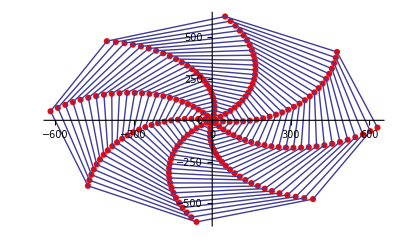

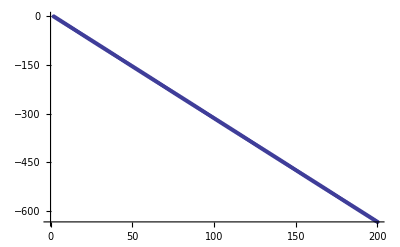

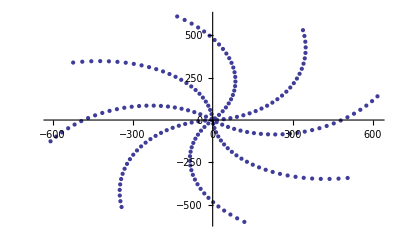

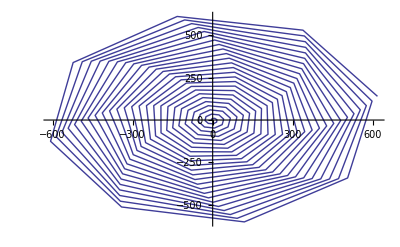

```mathematica
streem=OpenWrite["cardioidfx2rho2spiral4mar16no3"];
zeros={bestzero[2]};
data={};
jla={};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={k,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
Close[streem];
Print[ListPlot[jla]];
Print[ListPlot[data]];
Print[ListPlot[data,Joined->True]]
```

```mathematica
stream=OpenRead["cardioidfx2rho2spiral4mar16no3"];
list=ReadList[stream];
Close[stream];
el=Length[list];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=list[[j,2]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r2c1

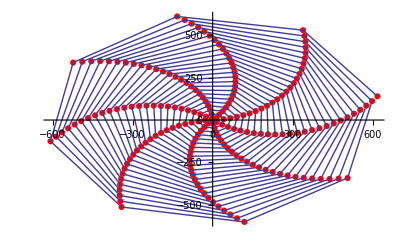

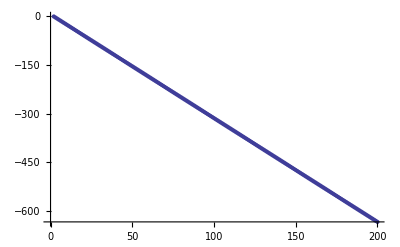

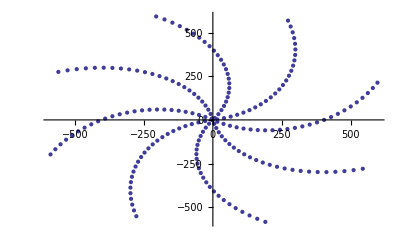

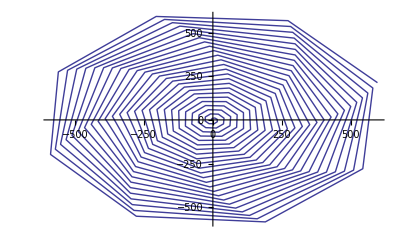

```mathematica
streem=OpenWrite["cardioidfx2rho3spiral4mar16no2"];
zeros={bestzero[3]};
data={};
jla={};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={k,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
Close[streem];
Print[ListPlot[jla]];
Print[ListPlot[data]];
Print[ListPlot[data,Joined->True]]
```

```mathematica
stream=OpenRead["cardioidfx2rho3spiral4mar16no2"];
list=ReadList[stream];
Close[stream];
el=Length[list];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=list[[j,2]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r3c1

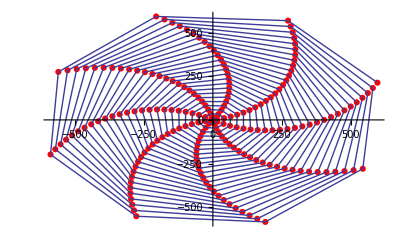

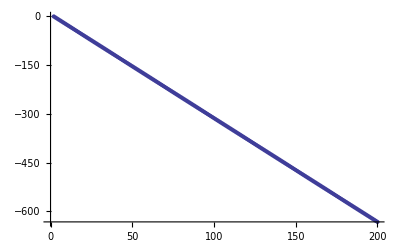

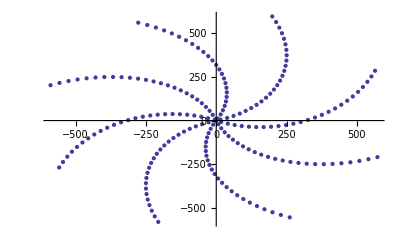

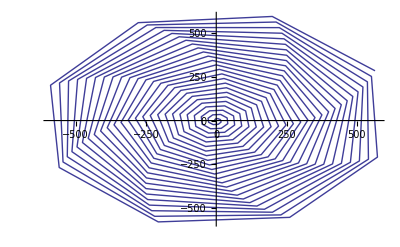

```mathematica
streem=OpenWrite["cardioidfx2rho4spiral4mar16no2"];
zeros={bestzero[4]};
data={};
jla={};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={k,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
Close[streem];
Print[ListPlot[jla]];
Print[ListPlot[data]];
Print[ListPlot[data,Joined->True]]
```

```mathematica
stream=OpenRead["cardioidfx2rho4spiral4mar16no2"];
list=ReadList[stream];
Close[stream];
el=Length[list];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=list[[j,2]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r4c1

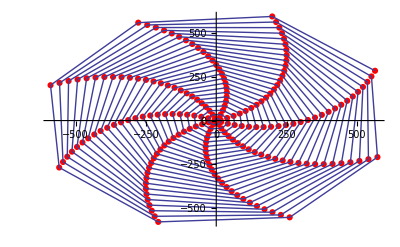

```mathematica
streem=OpenWrite["cardioidfx2rho5spiral9mar16no2"];
zeros={bestzero[5]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem];
el=Length[zeros];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=zeros[[j]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r5c1

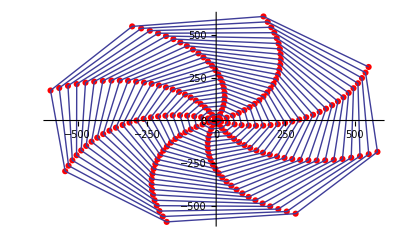

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

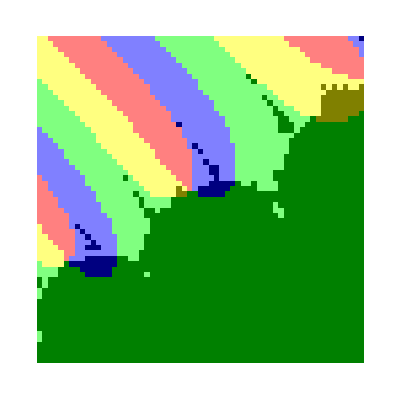

```mathematica
f[s_]:=zetaIterate[s,1]-s;
highbound=10^8;
lowbound=1/10^8;
center=-10.5+5*I;
searchradius=5;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

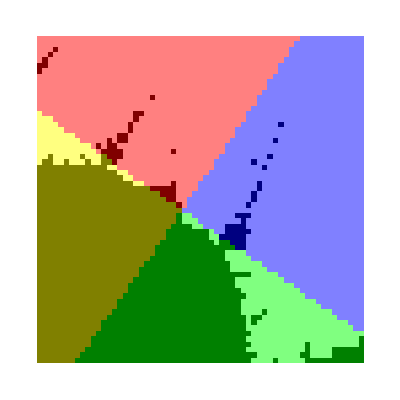

```mathematica
f[s_]:=zetaIterate[s,1]-s;
highbound=10^8;
lowbound=1/10^8;
center=-10.82+5.32*I;
searchradius=.01;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

```mathematica
precision=500;
f[s_]:=zetaIterate[s,1]-s;
startrange=.02;
rangedivider=2;
grain=20;
depth=20;
startcenter=-10.82+5.32*I;
fx=zeroFinder5[f,startcenter,startrange,rangedivider,grain,depth];
fxx=FindRoot[f[s],{s,fx[[1]]},WorkingPrecision->precision][[1,2]];
Print["fixed point   "];
Print[fxx];
Print["error"];
Print[zetaIterate[fxx,1]-fxx]
```

fixed point

-10.821148006023595165258300978174458683334306948910439783335119847596344627806213486173689753272823375348253816514335077250281675892370980696020094742339894962961688488019033552217785012031913567790012320434951985382919904469164051284499539962814351893014934743105577243142280410415970227449919061226855311870178679330506799704689019976583135068769659207257861901802301798747005928905446339489688059160957646778628877230186495888094434296561423993988830524687031180591277041099733441325058835705545223+5.3193414062340658907809379747379030592951148471258161086932194322073720573953920355447409035637101281565996871810770339298273062512503394990735219854728074426529706718259800951408730304935624163784026978666207031215347452049469801109956491495247984607812976463736911371240208531242473117608835935974308008427788529479016624326134047765215793628596331649080168736616236735174723525303502221017943998706632314766397741362309262632719976416077703158283483516693491695064431727526077646679011198552745814 ⅈ

error

0.+0. ⅈ

```mathematica
streem=OpenWrite["cardioidfx3rho1spiral9mar16"];
zeros={bestzero[1]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem]
```

cardioidfx3rho1spiral9mar16

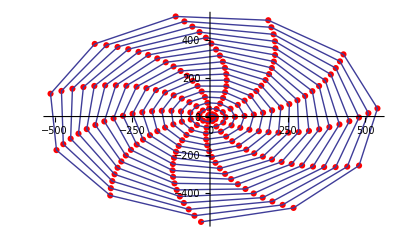

```mathematica
stream=OpenRead["cardioidfx3rho1spiral9mar16"];
list=ReadList[stream];
Close[stream];
el=Length[list];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=list[[j,2]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

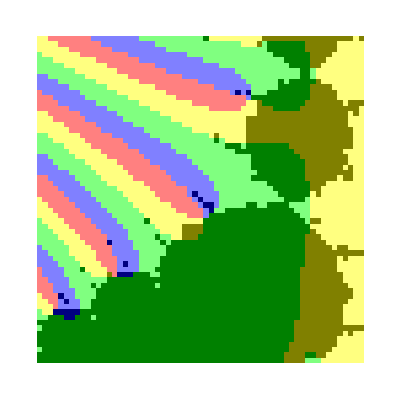

```mathematica
f[s_]:=zetaIterate[s,1]-s;
highbound=10^8;
lowbound=1/10^8;
center=-5.5+10*I;
searchradius=10;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

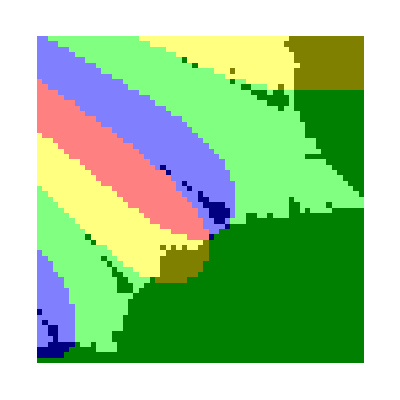

```mathematica
f[s_]:=zetaIterate[s,1]-s;
highbound=10^8;
lowbound=1/10^8;
center=-5.5+10*I;
searchradius=5;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

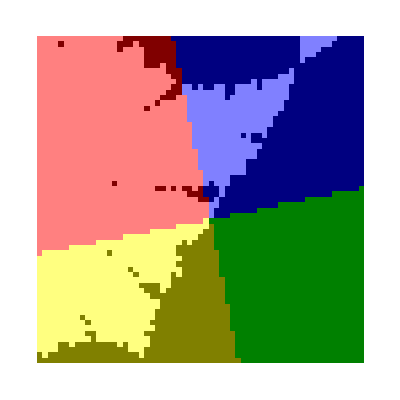

```mathematica
f[s_]:=zetaIterate[s,1]-s;
highbound=10^8;
lowbound=1/10^8;
center=-5.28+8.804*I;
searchradius=.01;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

```mathematica
precision=500;
f[s_]:=zetaIterate[s,1]-s;
startrange=.02;
rangedivider=2;
grain=20;
depth=20;
startcenter=-5.28+8.804*I;
fx=zeroFinder5[f,startcenter,startrange,rangedivider,grain,depth];
fxx=FindRoot[f[s],{s,fx[[1]]},WorkingPrecision->precision][[1,2]];
Print["fixed point   "];
Print[fxx];
Print["error"];
Print[zetaIterate[fxx,1]-fxx]
```

fixed point

-5.2793950307843170303114858336796243989728181480478160123779975981995490784460810805114368409073779568382301903634315636555647076720860391243559578310775624261359030131113554073691200899035546266170270934323989377516647988226115345529677670421282296003898216702930229915928317823421872479262268322217789798595011440602392307268150780212715241774502092380968902244861305397342255191446414359706579012637924930827159039868018623038203020391436392506396890849756260246786989618174756471226916906582543503+8.8027675740832589731484730202165154413652611010120156105363850126146179719289208919049162402169463057975389341509874501962361316250203877616458097719054347897619462299160694624177633458569647569740146343148764530464006343428940018334696506005766411633220142867511529633871211615428398413881654574356054209083414199778908824520311553493374813053470162209965732231474669292265567620776012621273963872526336766429858282738486028106518827088576795847884412744471507041973798073222107966597774317342111932 ⅈ

error

0.+0. ⅈ

```mathematica
streem=OpenWrite["cardioidfx4rho1spiral9mar16"];
zeros={bestzero[1]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem]
```

cardioidfx4rho1spiral9mar16

```mathematica
stream=OpenRead["cardioidfx4rho1spiral9mar16"];
list=ReadList[stream];
Close[stream];
el=Length[list];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=list[[j,2]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r1c2

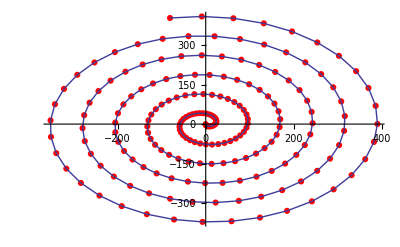

```mathematica
streem=OpenRead["cardioidfx4rho1spiral9mar16no2"];
ls=ReadList[streem];
Close[streem]
```

cardioidfx4rho1spiral9mar16no2

```mathematica
Length[ls]
```

199

```mathematica
ls[[1]]
```

{2,-5.03147371344314929861763824490084757347874904636307829840493486579220895616170695283778304769893714584919225299479354853989116841339061711176644071486011135239485007078799198695147174025284085993942280676355091778797705458286862483735033075173822358434328438143339948060129127561703766175258538855367+9.62515948660376912705103365064121230217027859481608006012014940426631879883330048661826582613817612690649053634694973911868483616956004725808193949637198679679750627036428006026510436271515603765589134606507288003351076915070127913016929418463998319616107653239718530311116995350819170904889430832219 ⅈ}

```mathematica
streem=OpenWrite["cardioidfx4rho2spiral9mar16no2"];
zeros={bestzero[2]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem];
el=Length[zeros];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=zeros[[j]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r2c2

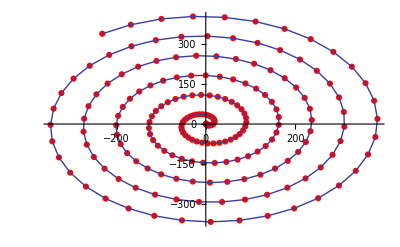

```mathematica
streem=OpenWrite["cardioidfx4rho3spiral9mar16no2"];
zeros={bestzero[3]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem];
el=Length[zeros];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=zeros[[j]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r3c2

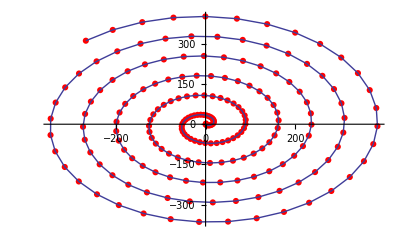

```mathematica
streem=OpenWrite["cardioidfx4rho4spiral9mar16no2"];
zeros={bestzero[4]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem];
el=Length[zeros];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=zeros[[j]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r4c2

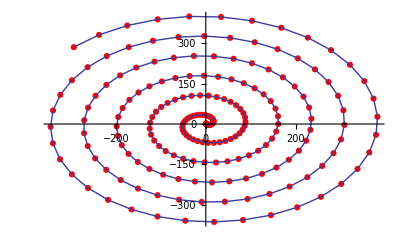

```mathematica
streem=OpenWrite["cardioidfx4rho5spiral9mar16no4"];
zeros={bestzero[5]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->300][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem];
el=Length[zeros];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=zeros[[j]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Show[p,pj]
```

## leaf5point2r5c2